```mathematica
<<Local`SrednickiInit`
```

e1410: IntegralOp[{{F[n_]}},a__]:>IntegralOp[xF[n],a (n-1)! DiracDelta[∑_(i=1)^n x[i]-1]]

e1427: IntegralOp[{{q}},(2 π)^-d (q^2)^a (D+q^2)^-b]→(2^-d D^(a-b+d/2) π^(-d/2) Gamma[-a+b-d/2] Gamma[a+d/2])/(Gamma[b] Gamma[d/2])

e1427s: IntegralOp[{{q}},(q^2)^a (D+q^2)^-b]→(D^(a-b+d/2) π^(d/2) Gamma[-a+b-d/2] Gamma[a+d/2])/(Gamma[b] Gamma[d/2])

e1426: Gamma[-n+ε]:>((-1)^n (1/ε-γ+∑_(k=1)^n 1/k))/(n!)

Problem 14.1

```mathematica
PR["Derive Feynman's formula (14.49), given (14.50) and (14.51): ",
e1450=Gamma[α[i_]] ->A[i]^α[i] IntegralOp[{{t[i], 0, Infinity}},t[i]^(α[i] - 1)/E^(t [i]A[i])] ,Yield,
e1450a=A[i_]^(-α[i_]) ->Gamma[α[i]]^-1 IntegralOp[{{t[i], 0, Infinity}},t[i]^(α[i] - 1)/E^(t [i]A[i])] ,and,
e1451=1==IntegralOp[{{s,0,∞}},DiracDelta[s-Sum[t[i],{i,1,n}]]],

"Applying these relations to the product of n 1/A's:  ",
tmp=Product[A[i]^(-α[i]),{i,1,n}],Yield,
tmp=tmp//.e1450a,

"\nSeparate the Products and switch order of Product and IntegralOp and letting t^n ","represent n-dimensional integration variables and introduce (14.51):",

tmp=tmp/.Product[a_ b_ ,d_]:>Product[a,d]Product[b,d];Yield;
tmp1=tmp/.Product[IntegralOp[{a_List},b_],c_List]:>IntegralOp[{{t^n,0,∞}},e1451[[2]]Product[b,c]],

"Switch order of integration:",
tmp=tmp1/.IntegralOp[a_List,IntegralOp[b_List,c_]d_]->IntegralOp[b,IntegralOp[a,c d]],

"\nChange integration variable, t[i]->s x[i] and manipulate:",Yield,
tmp=tmp/.IntegralOp[{{t^n,0,∞}},a_]:>IntegralOp[{{x[i],0,∞}},(a/.t[i]->s x[i])s^n];
tmp=tmp/.DiracDelta[a_]:>DiracDelta[a/.s->1];Yield;
tmp=tmp/.Product[a_ b_ ,d_]:>Product[a,d]Product[b,d];Yield;
tmp=tmp/.Product[Exp[-s a_],b_]:>Exp[-s Sum[a,b]];Yield;
tmp=tmp/.Power[s x[i],d_]->Power[s,d]Power[x[i],d];Yield;
tmp=tmp/.Product[a_ b_ ,d_List]:>Product[a,d]Product[b,d];Yield;
tmp=tmp/.Product[Power[s,d__],l_List]:>Power[s,Sum[d,l]];Yield;
tmp=tmp/.Sum[a_+b_,c_List]:>Sum[a,c]+Sum[b,c];Yield;
tmp=tmp/.
IntegralOp[a_List,IntegralOp[b_List,c_ DiracDelta[d_]]]->IntegralOp[b,IntegralOp[a,c ]DiracDelta[d]];Yield;
tmp=tmp/.IntegralOp[a_List,b_ Product[d_,f_]]->IntegralOp[a,b ]aProduct[d,f];Yield;
tmp2=tmp/.IntegralOp[{{s,0,∞}},a_ ]:>xIntegrate[a ,{s,0,∞}]
]
```

Derive Feynman's formula (14.49), given (14.50) and (14.51): Gamma[α[i_]]→A[i]^α[i] IntegralOp[{{t[i],0,∞}},ⅇ^(-A[i] t[i]) t[i]^(-1+α[i])]
→ A[i_]^(-α[i_])→IntegralOp[{{t[i],0,∞}},ⅇ^(-A[i] t[i]) t[i]^(-1+α[i])]/Gamma[α[i]] and 1==IntegralOp[{{s,0,∞}},DiracDelta[s-∑_(i=1)^n t[i]]]Applying these relations to the product of n 1/A's:  ∏_(i=1)^n A[i]^(-α[i])
→ ∏_(i=1)^n IntegralOp[{{t[i],0,∞}},ⅇ^(-A[i] t[i]) t[i]^(-1+α[i])]/Gamma[α[i]]
Separate the Products and switch order of Product and IntegralOp and letting t^n represent n-dimensional integration variables and introduce (14.51):IntegralOp[{{t^n,0,∞}},IntegralOp[{{s,0,∞}},DiracDelta[s-∑_(i=1)^n t[i]]] ∏_(i=1)^n ⅇ^(-A[i] t[i]) t[i]^(-1+α[i])] ∏_(i=1)^n 1/Gamma[α[i]]Switch order of integration:IntegralOp[{{s,0,∞}},IntegralOp[{{t^n,0,∞}},DiracDelta[s-∑_(i=1)^n t[i]] ∏_(i=1)^n ⅇ^(-A[i] t[i]) t[i]^(-1+α[i])]] ∏_(i=1)^n 1/Gamma[α[i]]
Change integration variable, t[i]->s x[i] and manipulate:
→ IntegralOp[{{x_i^i,0,∞}},aProduct[(x_i^i)^(-1+α[i]),{i,1,n}] DiracDelta[-1+∑_(i=1)^n x_i^i] xIntegrate[ⅇ^(-s ∑_(i=1)^n A[i] x_i^i) s^(∑_(i=1)^n α[i]),{s,0,∞}]] ∏_(i=1)^n 1/Gamma[α[i]]

```mathematica
PR["Do s integration.  There are simplification necessary to prevent the Integrate function from crashing:",Yield,
tmp3=tmp2/.Exp[-s a_]:>Exp[-s g[a]]/.s^a_->s^h[a];Yield;
pos=Position[tmp3,h[_]];
tmph=Extract[tmp3,pos][[1]];
tmp3=ReplacePart[tmp3,pos->H];
pos=Position[tmp3,g[_]];
tmpg=Extract[tmp3,pos][[1]];
tmp=ReplacePart[tmp3,pos->G];Yield;
tmp=tmp/.xIntegrate->Integrate;Yield;
tmp=Assuming[Re[G]>0&&Re[H]>-1,Refine[tmp]];Yield;
tmp3=tmp/.H->tmph/.G->tmpg/.h[a_]->a/.g[a_]->a,Yield,
"From (14.10):",Yield,
tmp4=tmp3/.IntegralOp[a_List,DiracDelta[b_] c_]->IntegralOp[{Subscript[F, n]},c/(n-1)!],Yield,
tmp4=tmp4/.Gamma[1+a_]->a Gamma[a];
tmp4=tmp4/.aProduct->Product,Imply,
"There is a difference between this result and (14.49) by a factor:"//CC,
Sum[α[i],{i,1,n}]/Sum[A[i]x[i],{i,1,n}]
]
```

Do s integration.  There are simplification necessary to prevent the Integrate function from crashing:
→ IntegralOp[{{x_i^i,0,∞}},aProduct[(x_i^i)^(-1+α[i]),{i,1,n}] DiracDelta[-1+∑_(i=1)^n x_i^i] Gamma[1+∑_(i=1)^n α[i]] (∑_(i=1)^n A[i] x_i^i)^(-1-∑_(i=1)^n α[i])] ∏_(i=1)^n 1/Gamma[α[i]]
→ From (14.10):
→ IntegralOp[{F_n},(aProduct[(x_i^i)^(-1+α[i]),{i,1,n}] Gamma[1+∑_(i=1)^n α[i]] (∑_(i=1)^n A[i] x_i^i)^(-1-∑_(i=1)^n α[i]))/((-1+n)!)] ∏_(i=1)^n 1/Gamma[α[i]]
→ IntegralOp[{F_n},(Gamma[∑_(i=1)^n α[i]] (∏_(i=1)^n (x_i^i)^(-1+α[i])) (∑_(i=1)^n A[i] x_i^i)^(-1-∑_(i=1)^n α[i]) ∑_(i=1)^n α[i])/((-1+n)!)] ∏_(i=1)^n 1/Gamma[α[i]]
⇒ There is a difference between this result and (14.49) by a factor:(∑_(i=1)^n α[i])/(∑_(i=1)^n A[i] x_i^i)

Problem 14.2

```mathematica
PR["Verify: ",
Define["e1423",Subscript[Ω, d]==(2 π^(d/2))/Gamma[d/2]],
"\nBreaking d-dimensional Gaussian integral into product of d single integrals: ",
tmp1=IntegralOp[{{x[i],-∞,∞}},Exp[-Sum[x[i]^2,{i,d}]]],yield,
tmp1=Integrate[Exp[-x^2],{x,-∞,∞}]^d,
"\nManipulate the spherical integral: ",
tmp=IntegralOp[{{Subscript[Ω, d]},{r}},r^(d-1)Exp[-r^2]],Yield,
tmp=SeparateIntVar1[{1,2},tmp];Yield;
tmp=tmp/.IntegralOp[{{r}},a_]:>Integrate[a,{r,0,∞},Assumptions->Re[d]>0];Yield;
tmp=tmp//IntegralOpMoveNVarOut;Yield;
tmp=tmp/.IntegralOp[{{Subscript[Ω, d]}},1]->Subscript[Ω, d],
"\nSubstituting (14.23) we show: ",
Solve[tmp1==tmp,{Subscript[Ω, d]}][[1,1]]
]
```

Verify: e1423: Ω_d==(2 π^(d/2))/Gamma[d/2]
Breaking d-dimensional Gaussian integral into product of d single integrals: ∫_{x[i],-∞,∞} [ⅇ^(-∑_i^d x[i]^2)] ⟶ π^(d/2)
Manipulate the spherical integral: ∫_({Ω_d}
{r}) [ⅇ^(-r^2) r^(-1+d)]
→ 1/2 Gamma[d/2] Ω_d
Substituting (14.23) we show: Ω_d→(2 π^(d/2))/Gamma[d/2]

Problem 14.3: In d-dimensions

```mathematica
PR1["Derive derivative operations on G[q^2].","POFF",
"We use the rules:",
Column[
sub={
PartialD[labels][qd[a_],qd[b_]]->δdu[a,b],PartialD[labels][qu[a_],qd[b_]]->PartialD[labels][qd[γ]guu[a,γ],qd[b]],PartialD[labels][guu[a_,b_],qd[c_]]->0,
guu[a_,b_]qd[b_]:>qu[a],
guu[a_,b_]qd[a_]:>qu[b],
PartialD[labels][qd[_],{qd[_],qd[_]}]->0,PartialD[labels][qd[_],{qd[_],qd[_]}]->0,
PartialD[labels][qd[_],{qd[_],qd[_],qd[_]}]->0,
PartialD[labels][qu[_],{qd[_],qd[_]}]->0,
PartialD[labels][qu[_],{qd[_],qd[_],qd[_]}]->0,
guu[a_,b_]:>guu[b,a]/;Order[a ,b]==-1
},Frame->All],
"PON",
New,"The 1st derivative: ",
d1=xPartialD[G[qd[ν]qu[ν]],qd[α]];
tmp=d1/.xPartialD->PartialD[labels];
tmp=tmp//.sub//KroneckerAbsorb[δ][#]&;
 tmpD1=d1->tmp,

New,"The 2nd derivative: ",
d2=xPartialD[G[qd[ν]qu[ν]],{qd[α],qd[β]}];
tmp=d2/.xPartialD->PartialD[labels];
tmp=tmp//.sub//KroneckerAbsorb[δ][#]&;
tmp=tmp//.sub//Expand;
tmpD2=d2->tmp,

New,"The 3rd derivative of: ",
d3=xPartialD[G[qd[ν]qu[ν]],{qd[γ],qd[α],qd[β]}];
tmp=d3/.xPartialD->PartialD[labels];
tmp=tmp//.sub//KroneckerAbsorb[δ][#]&;
tmpD3=d3->tmp//.sub//Expand,

New,"The 1st derivative: ",
dq1=xPartialD[qu[μ]G[qd[ν]qu[ν]],{qd[α]}];
tmp=dq1/.xPartialD->PartialD[labels];
tmp=tmp//.sub//KroneckerAbsorb[δ][#]&;
tmpDq1=dq1->tmp,

New,"The 1st derivative: ",
dq1a=xPartialD[qu[μ]qu[λ]G[qd[ν]qu[ν]],{qd[α]}];
tmp=dq1a/.xPartialD->PartialD[labels];
tmpDq1a=dq1a->(tmp//.sub//KroneckerAbsorb[δ][#]&),

New,"The 1st derivative of: ",
dq1b=xPartialD[qu[μ]qu[λ]qu[η]G[qd[ν]qu[ν]],{qd[α]}];
tmp=dq1b/.xPartialD->PartialD[labels];
tmp=tmp//.sub//KroneckerAbsorb[δ][#]&;
tmpDq1b=dq1b->tmp//Expand
]
```

Derive derivative operations on G[q^2].
● The 1st derivative: UnderBar[∂]_(q_α^α)[G[q_ν^ν q_ν^ν]]→2 q_α^α G'[q_ν^ν q_ν^ν]
● The 2nd derivative: UnderBar[∂]_{q_α^α,q_β^β}[G[q_ν^ν q_ν^ν]]→2 g_αβ^αβ G'[q_ν^ν q_ν^ν]+4 q_α^α q_β^β G''[q_ν^ν q_ν^ν]
● The 3rd derivative of: UnderBar[∂]_{q_γ^γ,q_α^α,q_β^β}[G[q_ν^ν q_ν^ν]]→4 g_βγ^βγ q_α^α G''[q_ν^ν q_ν^ν]+4 g_αγ^αγ q_β^β G''[q_ν^ν q_ν^ν]+4 g_αβ^αβ q_γ^γ G''[q_ν^ν q_ν^ν]+8 q_α^α q_β^β q_γ^γ G^(3)[q_ν^ν q_ν^ν]
● The 1st derivative: UnderBar[∂]_{q_α^α}[G[q_ν^ν q_ν^ν] q_μ^μ]→G[q_ν^ν q_ν^ν] g_αμ^αμ+2 q_α^α q_μ^μ G'[q_ν^ν q_ν^ν]
● The 1st derivative: UnderBar[∂]_{q_α^α}[G[q_ν^ν q_ν^ν] q_λ^λ q_μ^μ]→G[q_ν^ν q_ν^ν] (g_αμ^αμ q_λ^λ+g_αλ^αλ q_μ^μ)+2 q_α^α q_λ^λ q_μ^μ G'[q_ν^ν q_ν^ν]
● The 1st derivative of: UnderBar[∂]_{q_α^α}[G[q_ν^ν q_ν^ν] q_η^η q_λ^λ q_μ^μ]→G[q_ν^ν q_ν^ν] g_αμ^αμ q_η^η q_λ^λ+G[q_ν^ν q_ν^ν] g_αλ^αλ q_η^η q_μ^μ+G[q_ν^ν q_ν^ν] g_αη^αη q_λ^λ q_μ^μ+2 q_α^α q_η^η q_λ^λ q_μ^μ G'[q_ν^ν q_ν^ν]

```mathematica
PR["Show (14.52): ",
e1452=IntegralOp[{{qd[α]}},qu[μ]F[q^2]]==0,
" where: ",subq=q^2->qu[ν]qd[ν],Yield,
"Using the above relationship: ",tmpD1,
"and the correspondence: ",
subF=F[q^2]->2 G'[q^2],Yield,
tmp=e1452[[1]],yield,
tmp=tmp/.subF,yield,
tmp=tmp/.subq,yield,
tmp=tmp/.Reverse[tmpD1/.α->μ],"(",qd[α]," can be rotated so that one index is along μ and assuming ",G[q^2]⟶0," as ",qd[μ]⟶±∞," )",
yield,0,back,CR[" no Lorentz symmetry arguement."]
]
```

Show (14.52): ∫_{q_α^α} [F[q^2] q_μ^μ]==0 where: q^2→q_ν^ν q_ν^ν
→ Using the above relationship: UnderBar[∂]_(q_α^α)[G[q_ν^ν q_ν^ν]]→2 q_α^α G'[q_ν^ν q_ν^ν]and the correspondence: F[q^2]→2 G'[q^2]
→ ∫_{q_α^α} [F[q^2] q_μ^μ] ⟶ ∫_{q_α^α} [2 q_μ^μ G'[q^2]] ⟶ ∫_{q_α^α} [2 q_μ^μ G'[q_ν^ν q_ν^ν]] ⟶ ∫_{q_α^α} [UnderBar[∂]_(q_μ^μ)[G[q_ν^ν q_ν^ν]]](q_α^α can be rotated so that one index is along μ and assuming G[q^2]⟶0 as q_μ^μ⟶±∞ ) ⟶ 0 ⟵ no Lorentz symmetry arguement.

```mathematica
PR["Show (14.53): ",e1453=IntegralOp[{{qd[α]}},qu[μ]qu[ν]F[q^2]]==Subscript[C, 2] guu[μ,ν]IntegralOp[{{qd[α]}},q^2 F[q^2]],
New,"From above we have ",tmpD2,Yield,
(RuleX[tmpD2,qu[α_]qu[β_]G''[_]]/.G''->F/.G->F),check,

"\nContract with ",tmpg=gdd[μ,ν],Yield,
tmp=Map[# tmpg&,e1453];
tmp=tmp/.MoveIntOut1;
tmp=MetricSimplify[g][tmp],
" with ",sub={qd[ν]qu[ν]->q^2,gdu[a_,a_]->(d-2)},Imply,
tmp=tmp/.sub,Imply,
subc=Subscript[C, 2]->1/(d-2)
]
```

Show (14.53): ∫_{q_α^α} [F[q^2] q_μ^μ q_ν^ν]==∫_{q_α^α} [q^2 F[q^2]] C_2 g_μν^μν
● From above we have UnderBar[∂]_{q_α^α,q_β^β}[G[q_ν^ν q_ν^ν]]→2 g_αβ^αβ G'[q_ν^ν q_ν^ν]+4 q_α^α q_β^β G''[q_ν^ν q_ν^ν]
→ {F[_] q_α_^α_ q_β_^β_→1/4 (UnderBar[∂]_{q_α^α,q_β^β}[F[q_ν^ν q_ν^ν]]-2 g_αβ^αβ F'[q_ν^ν q_ν^ν])}⟵CHECK
Contract with g_μν^μν
→ ∫_{q_α^α} [F[q^2] q_ν^ν q_ν^ν]==∫_{q_α^α} [q^2 F[q^2] C_2 g_νν^νν] with {q_ν^ν q_ν^ν→q^2,g_a_a_^a_a_→-2+d}
⇒ ∫_{q_α^α} [q^2 F[q^2]]==∫_{q_α^α} [(-2+d) q^2 F[q^2] C_2]
⇒ C_2→1/(-2+d)

```mathematica
β
```

```mathematica
tmp=e1453/.subc
"From:"
tmpD2/.qu[a_]qd[a_]->q^2/.α->ν//Expand
tmpD1
```

IntegralOp[{d^d q},F[q^2] q_μ^μ q_ν^ν]==(IntegralOp[{d^d q},q^2 F[q^2]] g_μν^μν)/(-2+d)

From:

g_μν^μν G'[q^2]+g_νμ^νμ G'[q^2]+4 q_μ^μ q_ν^ν G''[q^2]

PartialD[{x,δ,g,Γ}][G[q_ν^ν q_ν^ν],q_μ^μ]→2 q_μ^μ G'[q_ν^ν q_ν^ν]

Problem 14.4

```mathematica
DefPrint["e1436",Π[k^2]==α/2 IntegralOp[{{x,0,1}},D Log[D/m^2]-(α/6(1/ε+Log[μ/m]+1/2)+A)k^2-(α(1/ε+Log[μ/m]+1/2)+B)m^2]]
DefPrint["e1437",A->-α/6(1/ε+Log[μ/m]+1/2+Subscript[κ, A])]
DefPrint["e1438",B->-α(1/ε+Log[μ/m]+1/2+Subscript[κ, B])]
tmp=e1436/.e1437/.e1438//Simplify
"This is e1439"
DefPrint["e1439",tmp]
```

e1436: Π[k^2]==1/2 α IntegralOp[{{x,0,1}},D Log[D/m^2]-k^2 (A+1/6 α (1/2+1/ε+Log[μ/m]))-m^2 (B+α (1/2+1/ε+Log[μ/m]))]

e1437: A→-1/6 α (1/2+1/ε+Log[μ/m]+κ_A)

e1438: B→-α (1/2+1/ε+Log[μ/m]+κ_B)

α IntegralOp[{{x,0,1}},D Log[D/m^2]+1/6 k^2 α κ_A+m^2 α κ_B]==2 Π[k^2]

This is e1439

e1439: α IntegralOp[{{x,0,1}},D Log[D/m^2]+1/6 k^2 α κ_A+m^2 α κ_B]==2 Π[k^2]

Try to integrate e1439

```mathematica
e1439/.D->m^2+k^2 x(1-x);
t1439=tmp=%/.IntegralOp[a_List,b_]:>xIntegrate[(b//PowerExpand),a[[1]]]
tmpi=Extract[tmp,Position[tmp,xIntegrate[__]]][[1,1]];
"total integrand too difficult for online, so break apart"
tmpx=Select[tmpi,!FreeQ[#,x]&]
tmpx0=Select[tmpi,FreeQ[#,x]&];
tmpfac=tmpx[[1]];
tmpx/.tmpfac->F//Expand;
tmpx=%/.F->tmpfac;
tmpx[[2]];
tmpx0I=tmp[[1]]/.xIntegrate[a_,b_]:>Integrate[tmpx0,b]
tmp[[1]]/.xIntegrate[a_,b_]:>Integrate[tmpx[[1]],b];
tmp[[1]]/.xIntegrate[a_,b_]:>xIntegrate[tmpx[[2]],b];(*no local solution*)
```

α xIntegrate[(m^2+k^2 (1-x) x) (-2 Log[m]+Log[m^2+k^2 (1-x) x])+1/6 k^2 α κ_A+m^2 α κ_B,{x,0,1}]==2 Π[k^2]

total integrand too difficult for online, so break apart

(m^2+k^2 (1-x) x) (-2 Log[m]+Log[m^2+k^2 (1-x) x])

α (1/6 k^2 α κ_A+m^2 α κ_B)

```mathematica
"Integral of above integrand from online resource:"
tmp=(-6*(-k^2-4*m^2)^(3/2)*ArcTan[(k*(-1+2*x))/Sqrt[-k^2-4*m^2]]+k*(-2*x*(24*m^2+k^2*(3+6*x-4*x^2))-12*x*(6*m^2+k^2*(3-2*x)*x)*Log[m]-3*(6*m^2*(1-2*x)+k^2*(1-6*x^2+4*x^3))*Log[m^2-k^2*(-1+x)*x]))/(36*k);
tmp1=tmp/.x->1;
tmp0=tmp/.x->0;
tmp1-tmp0//Simplify;
tmpxI=α %
```

Integral of above integrand from online resource:

-1/(18 k)α (6 (-k^2-4 m^2)^(3/2) ArcTan[k/(√(-k^2-4 m^2))]+k (5 k^2+24 m^2+6 (k^2+6 m^2) Log[m]-3 (k^2+6 m^2) Log[m^2]))

Constrain κ_A, κ_B for Π ,Π' values at k^2==-m^2

```mathematica
s1439=t1439[[2]]->tmpxI+tmpx0I//ExpandAll//FullSimplify;
p1439a=s1439/.k^2->-m^2/.k->√(-m^2)//Simplify
```

2 Π[-m^2]→-1/18 m^2 α (19-3 √3 π+30 Log[m]-15 Log[m^2]+3 α κ_A-18 α κ_B)

```mathematica
D[s1439,k];
Map[#/(4 k)&,%]//Simplify;
p1439b=%/.k^2->-m^2/.k->√(-m^2)//Simplify
```

Π'[-m^2]→1/36 α (-14+3 √3 π-6 Log[m]+3 Log[m^2]+3 α κ_A)

Solve Π==0 and Π'==0 for κ_A and κ_B

```mathematica
{p1439a[[2]]==0,
p1439b[[2]]==0};
Solve[%,{Subscript[κ, A],Subscript[κ, B]}][[1]]
```

{κ_B→-(-11+2 √3 π-12 Log[m]+6 Log[m^2])/(6 α),κ_A→-(-14+3 √3 π-6 Log[m]+3 Log[m^2])/(3 α)}

```mathematica
DefPrint["e1427",IntegralOp[{{q}},1/(2 π)^d((q^2)^a)/((q^2+D)^b)]->(Gamma[b-a-d/2]Gamma[a+d/2])/((4 π)^(d/2)Gamma[b]Gamma[d/2])D^(-(b-a-d/2))]
```

e1427: IntegralOp[{{q}},(2 π)^-d (q^2)^a (D+q^2)^-b]→(2^-d D^(a-b+d/2) π^(-d/2) Gamma[-a+b-d/2] Gamma[a+d/2])/(Gamma[b] Gamma[d/2])

Problem 14.5

The O(λ) propagator in the φ^4 theory.
There is only one diagram that contributes at this level, a single loop tangent to two external lines.

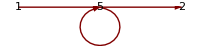

```mathematica
GraphPlot[{{1->5,k[1]},{5->5,q[1]},{5->2,k[1]}},VertexLabeling->True,DirectedEdges-> True,MultiedgeStyle->.5,VertexCoordinateRules->{1->{0,0},2->{3,0},5->{1.5,0}} ,ImageSize->200]
```

The perturbation schema for the path integral formulation from (9.6), (9.7)

```mathematica
tmpz=Z[J]->Exp[ⅈ(-λ/24)IntegralOp[{{x}},(1/ⅈ δOp[J])^4]] Subscript[Z, 0][J]
tmpz0=Subscript[Z, 0][J]->Exp[ⅈ/2 IntegralOp[{{x},{y}},J[x].Δ[x-y].J[y]]]
```

Z[J]→ⅇ^(-1/24 ⅈ λ IntegralOp[{{x}},δOp[J]^4]) Z_0[J]

Z_0[J]→ⅇ^(1/2 ⅈ IntegralOp[{{x},{y}},J[x].Δ[x-y].J[y]])

Series expansion of Exp in Z[]'s

```mathematica
PR[
tmp=tmpz/.IntegralOp[a__]->X IntegralOp[a];
tmp=tmp[[1]]->Series[tmp[[2]],{X,0,1}]//Normal;
"Z[J] term to n->1: ",
tmpz1a=tmpz1=tmp/.X->1,
tmp=tmpz0/.IntegralOp[a__]->X IntegralOp[a];
tmp=tmp[[1]]->Series[tmp[[2]],{X,0,3}]//Normal;
tmpz01=tmp/.X->1;
tmpz01a=tmpz01/.Power[IntegralOp[a__],n_]:>DotPower[IntegralOp[a],n];
"Z_0 terms to n=3:",
Column[Apply[List,tmpz01a[[2]]],Frame->All,ItemSize->{30,2}]
]
```

Z[J] term to n->1: Z[J]→Z_0[J]-1/24 ⅈ λ IntegralOp[{{x}},δOp[J]^4] Z_0[J]Z_0 terms to n=3:1
-1/8 IntegralOp[{{x},{y}},J[x].Δ[x-y].J[y]].IntegralOp[{{x},{y}},J[x].Δ[x-y].J[y]]
-1/48 ⅈ IntegralOp[{{x},{y}},J[x].Δ[x-y].J[y]].IntegralOp[{{x},{y}},J[x].Δ[x-y].J[y]].IntegralOp[{{x},{y}},J[x].Δ[x-y].J[y]]
1/2 ⅈ IntegralOp[{{x},{y}},J[x].Δ[x-y].J[y]]

The O(λ) term with 2 external points will need a  J^6  factor.

```mathematica
PR[
"Due to the δOp[J]^4 factor in Z[J]:","\n",
tmpz1a,
"\nthe term with only 2 resulting external lines will use the Z_0[J] expression with J^6 factors:",Yield,
tmpz01a[[2,3]]
]
```

Due to the δOp[J]^4 factor in Z[J]:
Z[J]→Z_0[J]-1/24 ⅈ λ IntegralOp[{{x}},δOp[J]^4] Z_0[J]
the term with only 2 resulting external lines will use the Z_0[J] expression with J^6 factors:
→ -1/48 ⅈ IntegralOp[{{x},{y}},J[x].Δ[x-y].J[y]].IntegralOp[{{x},{y}},J[x].Δ[x-y].J[y]].IntegralOp[{{x},{y}},J[x].Δ[x-y].J[y]]

The correspondence to (14.4) where the Π is ( the integral doesn't have k^2dependence):

```mathematica
PR[x144=ⅈ Π[k^2]->1/2(ⅈ λ)^1(-ⅈ)IntegralOp[{{h}},Δ[h^2]/(2 π)^d]-ⅈ(A k^2+B m^2),
"where h is d-dimensional."
]
```

ⅈ Π[k^2]→-ⅈ (A k^2+B m^2)+1/2 λ IntegralOp[{{h}},(2 π)^-d Δ[h^2]]where h is d-dimensional.

Apply definition of free propagator and integrate. Determine A,B from Π[-m^2]==0 and  Π'[-m^2]==0 conditions.

```mathematica
PR[
"From: ",
tmp144=x144/.Δ[a_]->1/(a+m^2-ⅈ ϵ),
"\nUsing Wick rotation (I) and leaving the integral indefinite for {h,0,∞}:",Yield,
tmp=tmp144/.IntegralOp[a_List,b_]:>I Integrate[b h^(d-1),h,Subscript[Ω, d]];
tmp=tmp/.ϵ->0,
"The Π[-m^2]==0 condition",
tmpa=tmp/.k^2->-m^2;and,
"Π'[-m^2]==0 condition:",Yield;
tmpb=Map[D[#,k2]&,(tmp/.k^2->k2)]/.k2->-m^2;Yield;
tmp={tmpa[[2]]==0,tmpb[[2]]==0};Yield,
subAB=Solve[tmp,{A,B}][[1]]/.Apply[Rule,e1423],

"\nEvaluation of B over the integral limits {h,0,∞} for d->4: ",
tmp=B/.subAB/.d->4,

tmp=tmp/.h->1/hi;
"  is not finite",Yield,
Limit[tmp,hi->0]
]
```

From: ⅈ Π[k^2]→-ⅈ (A k^2+B m^2)+1/2 λ IntegralOp[{{h}},(2 π)^-d/(h^2+m^2-ⅈ ϵ)]
Using Wick rotation (I) and leaving the integral indefinite for {h,0,∞}:
→ ⅈ Π[k^2]→-ⅈ (A k^2+B m^2)+ⅈ 2^(-1-d) π^-d λ (h^d/(d m^2)-(h^(2+d) Hypergeometric2F1[1,(2+d)/2,1+(2+d)/2,-h^2/m^2])/((2+d) m^4)) Ω_dThe Π[-m^2]==0 condition and Π'[-m^2]==0 condition:
→ {B→(2^-d h^d π^(-d/2) λ (2 m^2+d m^2-d h^2 Hypergeometric2F1[1,(2+d)/2,1+(2+d)/2,-h^2/m^2]))/(d (2+d) m^6 Gamma[d/2]),A→0}
Evaluation of B over the integral limits {h,0,∞} for d->4: (h^4 λ (6 m^2-(6 (h^4 m^2-2 h^2 m^4+2 m^6 Log[1+h^2/m^2]))/h^4))/(384 m^6 π^2)  is not finite
→ (λ DirectedInfinity[Sign[m]^4])/Sign[m]^6

Alternatively applying (14.27) to above integral for d->4-ϵ in the dimensional regularization method.

```mathematica
PR["Apply (14.27) for: ",
sub={a->0,b->1,d->4-ε} ,
" to (14.27): ",
tmp=e1427s/.sub//Simplify,
" then apply (14.26) ",Yield,
sub=e1426/.{n->1,ε->ε/2};
tmp=tmp/.sub,
subtmp=tmp/.sub/.{D->m^2,q->h};
" apply Wick rotation (I): ",Yield,
tmp=tmp144/.{ϵ->0,d->4}/.IntegralOp[a_,b_]:>I IntegralOpMoveNVarOut[a,b],Yield,
tmpa=tmp/.subtmp/.a_^b_:>a^(b/.ε->0)
]
```

Apply (14.27) for: {a→0,b→1,d→4-ε} to (14.27): IntegralOp[{{q}},1/(D+q^2)]→D^(1-ε/2) π^(2-ε/2) Gamma[-1+ε/2] then apply (14.26) 
→ IntegralOp[{{q}},1/(D+q^2)]→D^(1-ε/2) π^(2-ε/2) (-1+γ-2/ε) apply Wick rotation (I): 
→ ⅈ Π[k^2]→-ⅈ (A k^2+B m^2)+(ⅈ λ IntegralOp[{{h}},1/(h^2+m^2)])/(32 π^4)
→ ⅈ Π[k^2]→-ⅈ (A k^2+B m^2)+(ⅈ m^2 (-1+γ-2/ε) λ)/(32 π^2)

Set Π[k^2->-m^2]==0 and Π'[k^2->-m^2]==0  and solve for A, B

```mathematica
PR[
tmpam=tmpa/.k^2->-m^2;
tmpb=tmpa/.k^2->k2;
tmpb=D[tmpb,k2];
tmp={tmpam[[2]]==0,tmpb[[2]]==0};
tmp=Solve[tmp,{A,B}][[1]]//Simplify;
"Simplify B: set exponential ε ->0 and ",
tmpb=tmp[[1,2]]/.a_^b_:>a^(b/.ε->0);
tmpb=Series[tmpb,{ε,0,1}]//Normal;
tmp[[1,2]]=Collect[tmpb,{π^2 λ}];
"we are left with",Yield,
subABdim=tmp,Imply,
tmpa/.subABdim//Simplify
]
Save["14.save",{ subAB,subABdim}]
```

Simplify B: set exponential ε ->0 and we are left with
→ {B→-λ/(16 π^2 ε)+(-λ+γ λ)/(32 π^2),A→0}
⇒ ⅈ Π[k^2]→0

Problem 14.6

Problem 14.7

```mathematica
DefPrint["e1453",L[q,q̇]->1/2 Z (q̇)^2-1/2 Subscript[Z, ω] ω^2 q^2-Subscript[Z, λ] λ ω^3 q^4]
```

e1453: L[q,q̇]→(Z (q̇)^2)/2-q^4 λ ω^3 Z_λ-1/2 q^2 ω^2 Z_ω

```mathematica
tmpH=H->Subscript[H, 0]+Subscript[H, 1];
tmpH0=Subscript[H, 0]->1/2 P^2+1/2 ω^2 Q^2;
tmpC=MCommutator[Q,P]==ⅈ;
tmpP=P->D[L[q,q̇],q̇]//HoldOp[D];
tmpP=tmpP/.e1453//ReleaseHold
tmpH=H->P q̇-L[q,q̇]
tmpH=tmpH/.e1453/.tmpP
```

P→Z q̇

H→-L[q,q̇]+P q̇

H→(Z (q̇)^2)/2+q^4 λ ω^3 Z_λ+1/2 q^2 ω^2 Z_ω

Identify q,q̇ with Q, P/Z

```mathematica
tmpP1=tmpP[[2]]/Z->tmpP[[1]]/Z;
tmpHa=tmpH/.tmpP1/.q->Q
```

H→P^2/(2 Z)+Q^4 λ ω^3 Z_λ+1/2 Q^2 ω^2 Z_ω

Subtract H0

```mathematica
tmpHa;
Map[#-Subscript[H, 0]&,%];
%/.Subscript[H, 0]->P^2/2+ω^2 Q^2/2;
%//Collect[#,{P,Q},Simplify]&
tmpH1=H1->%[[2]]
```

H-P^2/2-(Q^2 ω^2)/2→1/2 P^2 (-1+1/Z)+Q^4 λ ω^3 Z_λ+1/2 Q^2 ω^2 (-1+Z_ω)

H1→1/2 P^2 (-1+1/Z)+Q^4 λ ω^3 Z_λ+1/2 Q^2 ω^2 (-1+Z_ω)

```mathematica
tmpH1/.Subscript[Z, λ]->1/.Subscript[Z, ω]->1+B/.Z->1+A//Collect[#,{P,Q},Simplify]&
```

H1→-(A P^2)/(2+2 A)+1/2 B Q^2 ω^2+Q^4 λ ω^3

==============
Rayleigh-Schodinger perturbation technique to define O(λ) corrections to eigenvalues E=E_0+dE, and eigenstates, |Ω>=|0>+d|0>.  Keep only first order in λ.

```mathematica
(*function to keep non-commuting terms in proper order.*)DotForm[a_]:=dotRetain[{H,H0,H1,⟨__|,|__⟩,Sum[_,_],P,Q},a]
```

```mathematica
Print["Define the Hamiltonian as the sum of the pure harmonic oscillator Hamiltonian, H0, and the perturbative Hamiltonian, H1, where λ is the smallness factor",Yield,
subH=H->H0+λ H1,"\nand energy eigenvalues for perturbed and unperturbed states is represented by",Yield,
En[s,j,d],", where s={0,p} for the {unperturbed,perturbed} states and j={0,1,...} indicates energy levels, and d, if present, indicates d-th order expansion in λ." ,"\nThe eigenstates are",Yield,
|{s,j,d}⟩,"\n(The {} is needed because Quantum Notation commutes the BraKet parameters.)"
];

Print["Eigenvalues correction O[λ]-level\n",
"Full equation for level j: ",
tmp=H.|{p,j}⟩->En[p,j]|{p,j}⟩,Imply,
tmp=tmp/.subH;
(*expand in terms of unperturbed quantities.*)
subp={|{p,j_}⟩->|{0,j}⟩+λ|{0,j,1}⟩,En[p,j_]:>En[0,j]+λ En[0,j,1]};
tmp=tmp/.subp//DotForm[#]&;
tmp=tmp/.λ^2->0/.H0.|{0,j_}⟩->En[0,j] |{0,j}⟩;
tmp1=Map[Coefficient[#,λ,0]&,tmp](*zero order term*);
"First order:  ",
tmp1=Map[Coefficient[#,λ,1]&,tmp](*first order term*),Imply,
tmp=Map[⟨{0,j}|.#&,tmp1]//DotForm[#]&;
tmp=tmp/.⟨{0,j}|.H0->En[0,j] ⟨{0,j}|//DotForm[#]&;
tmp=tmp/.⟨a_|.|a_⟩->1;
tmpE11=Apply[Equal,tmp]//Simplify(*first order energy correction.*);
subEj1=tmpE11[[1]]->tmpE11[[2]]
];
```

Define the Hamiltonian as the sum of the pure harmonic oscillator Hamiltonian, H0, and the perturbative Hamiltonian, H1, where λ is the smallness factor
→ H→H0+H1 λ
and energy eigenvalues for perturbed and unperturbed states is represented by
→ En[s,j,d], where s={0,p} for the {unperturbed,perturbed} states and j={0,1,...} indicates energy levels, and d, if present, indicates d-th order expansion in λ.
The eigenstates are
→ |{s,j,d}⟩
(The {} is needed because Quantum Notation commutes the BraKet parameters.)

Eigenvalues correction O[λ]-level
Full equation for level j: H.|{p,j}⟩→En[p,j] |{p,j}⟩
⇒ First order:  H0.|{0,j,1}⟩+H1.|{0,j}⟩→En[0,j,1] |{0,j}⟩+En[0,j] |{0,j,1}⟩
⇒ ⟨{0,j}|.H1.|{0,j}⟩→En[0,j,1]

```mathematica
Print["Assume unit[n] is a decomposition of unity where |{0,n}⟩ is singled out and orthogonal to all other vectors.",
unit[n_]:=Sum[|{0,k}⟩.⟨{0,k}|,{k,k≠n}]+|{0,n}⟩.⟨{0,n}|;
"For example, ",
unit[1]
];
```

Assume unit[n] is a decomposition of unity where |{0,n}⟩ is singled out and orthogonal to all other vectors.For example, |{0,1}⟩.⟨{0,1}|+∑_k^(k≠1) |{0,k}⟩.⟨{0,k}|

Compute purturbed eigenstates--Decompose first order equation into eigenstates

```mathematica
Print["Compute perturbed Hamiltonian on |{0,j}⟩: ",Yield,
tmp=H1.|{0,j}⟩==unit[j].H1.|{0,j}⟩;Yield;
(*apply above expression for E1.*)
tmp1a=tmp/.subEj1//DotForm[#]&;
(*subtract O(λ) H equation*)
tmp=tmp1a[[1]]-tmp1[[1]]==tmp1a[[2]]-tmp1[[2]];Yield;
(*assume non-degenerate states, apply unperturbed eigenstates <k|*)
tmp=Map[⟨{0,k}|.#&,tmp]/.⟨{0,k}|.Sum[_,_]->⟨{0,k}|//DotForm[#]&;Yield;
tmp=tmp/.⟨{0,k}|.H0->En[0,k] ⟨{0,k}|//DotForm[#]&;Yield;
tmp=tmp/.⟨{0,k}|.|{0,j}⟩->0;(*eigenstates non-degenerate*)
sub=Solve[tmp,⟨{0,k}|.|{0,j,1}⟩][[1]];Yield;
tmp=|{0,j,1}⟩==unit[j].|{0,j,1}⟩(*spectral decompose*);
tmp=tmp/.Sum[a_,b_].|{0,j,1}⟩->Sum[a.|{0,j,1}⟩,b]/.sub;Yield;
tmpeigen=tmp/.⟨{0,j}|.|{0,j,1}⟩->0(*assume orthogonal.*)
];
```

Compute perturbed Hamiltonian on |{0,j}⟩: 
→ |{0,j,1}⟩==∑_k^(k≠j) |{0,k}⟩.⟨{0,k}|.H1.|{0,j}⟩/(En[0,j]-En[0,k])

Define Q,P operations on eigenvectors.

```mathematica
subQP={Q->(a+SuperDagger[a])/√(2 ω),P->ⅈ √(ω/2)(SuperDagger[a]-a),a.|{s_,n_}⟩:>√n|{s,n-1}⟩,SuperDagger[a].|{s_,n_}⟩:>√(n+1)|{s,n+1}⟩,⟨a_|.|a_⟩->1,⟨a_|.|b_⟩:>KroneckerDelta[a,b]};
OpQP[exp_]:=Module[{tmp=exp,tmpl=0},
While[tmpl=!=tmp,tmpl=tmp; tmp=tmp//.subQP;tmp=dotRetain[{a,SuperDagger[a],|_⟩,⟨_|},tmp]];
tmpl];
Print["With these definitions:\n",
tmp=(Q.P-P.Q).|{0,j}⟩;tmp->OpQP[tmp],"\n",
tmp=Q.|{0,0}⟩;tmp->OpQP[tmp],"\n",
tmp=P.|{0,0}⟩;tmp->OpQP[tmp],"\n",
tmp=⟨{0,0}|.P.P.|{0,0}⟩;tmp->OpQP[tmp]
];
```

With these definitions:
(-P.Q).|{0,j}⟩+Q.P.|{0,j}⟩→ⅈ |{0,j}⟩
Q.|{0,0}⟩→(|{0,1}⟩)/(√2 √ω)
P.|{0,0}⟩→(ⅈ √ω |{0,1}⟩)/(√2)
⟨{0,0}|.P.P.|{0,0}⟩→ω/2

The eigenvalue correction for each unperturbed eigenvalue for the provided conditions

```mathematica
Print["The perturbation to the unperturbed energy states:\n",
tmp=subEj1/.tmpH1/.Subscript[Z, ω]->1+B/.Subscript[Z, λ]->1/.Z->1+A/.P^n_:>DotPower[P,n]/.Q^n_:>DotPower[Q,n],Yield,
tmp=tmp//DotForm[#]&;Yield;
tmp=OpQP[tmp];Yield;
"\nThen to O(λ) with the substitutions: ",sub={A->Subscript[κ, A] λ,B->Subscript[κ, B] λ}," the perturbation for the j-th level becomes",Imply,
perturbEigenvalueJ=Series[tmp[[1]]/.sub,{λ,0,1}]//Normal//Simplify,
"\nFor example j=0: ",
perturbEigenvalueJ/.j->0
];
```

The perturbation to the unperturbed energy states:
⟨{0,j}|.(1/2 (-1+1/(1+A)) P.P).|{0,j}⟩+⟨{0,j}|.(1/2 B ω^2 Q.Q).|{0,j}⟩+⟨{0,j}|.(λ ω^3 Q.Q.Q.Q).|{0,j}⟩→En[0,j,1]
→ 
Then to O(λ) with the substitutions: {A→λ κ_A,B→λ κ_B} the perturbation for the j-th level becomes
⇒ 1/4 λ ω (3+6 j+6 j^2-(1+2 j) κ_A+(1+2 j) κ_B)
For example j=0: 1/4 λ ω (3-κ_A+κ_B)

The eigenvector correction with the above perturbation.

```mathematica
Print[tmp=tmpeigen,Imply,
tmp=tmp/.tmpH1/.Subscript[Z, ω]->1+B/.Subscript[Z, λ]->1/.Z->1+A/.P^n_:>DotPower[P,n]/.Q^n_:>DotPower[Q,n],Imply;
tmp=tmp//DotForm[#]&;Yield;
tmp=OpQP[tmp];Yield;
tmp=tmp/.KroneckerDelta[{0,j},{0,k}]->0;
tmp=tmp/.KroneckerDelta[{0,a_},{0,b_}]->KroneckerDelta[a,b];
tmp=tmp/.KroneckerDelta[j,k]->0;
tmp=tmp//SumKronecker;Yield;
tmp=tmp/.Sum[a_,b_]->a;Yield;
"\nThen to O(λ) with the substitutions: ",sub={A->Subscript[κ, A] λ,B->Subscript[κ, B] λ},Yield,
tmp=tmp/.sub;
perturbEigenvector=Series[tmp,{λ,0,1}]//Normal//Simplify
];
```

|{0,j,1}⟩==∑_k^(k≠j) |{0,k}⟩.⟨{0,k}|.H1.|{0,j}⟩/(En[0,j]-En[0,k])
⇒ |{0,j,1}⟩==∑_k^(k≠j) |{0,k}⟩.(⟨{0,k}|.(1/2 (-1+1/(1+A)) P.P).|{0,j}⟩+⟨{0,k}|.(1/2 B ω^2 Q.Q).|{0,j}⟩+⟨{0,k}|.(λ ω^3 Q.Q.Q.Q).|{0,j}⟩)/(En[0,j]-En[0,k])
Then to O(λ) with the substitutions: {A→λ κ_A,B→λ κ_B}
→ |{0,j,1}⟩==1/4 λ ω ((√(-3+j) √(-2+j) √(-1+j) √j |{0,-4+j}⟩)/(-En[0,-4+j]+En[0,j])-(√(-1+j) √j (-2+4 j+κ_A+κ_B) |{0,-2+j}⟩)/(En[0,-2+j]-En[0,j])+√(1+j) √(2+j) (((6+4 j+κ_A+κ_B) |{0,2+j}⟩)/(En[0,j]-En[0,2+j])+(√(3+j) √(4+j) |{0,4+j}⟩)/(En[0,j]-En[0,4+j])))

Evaluate the ground and first excited states of the full system where En[0,1]-En[0,0]=ω

```mathematica
(*perturbative eigenvalue function*)
En[0,k_,1]:=perturbEigenvalueJ/.j->k;
Print["The defined excitation energy, ω, ",Yield,
tmp=0==En[0,1,1]-En[0,0,1]//Simplify,Yield,
eq1=Solve[tmp,Subscript[κ, A]][[1]]/.Rule->Equal
];
```

The defined excitation energy, ω, 
→ λ ω (-6+κ_A-κ_B)==0
→ {κ_A==6+κ_B}

```mathematica
(*perturbative eigenvector function*)eigenVector[k_]:=perturbEigenvector/.j->k;
subV[k_]:=|{p,k}⟩->|{0,k}⟩+eigenVector[k][[2]];
subVt[k_]:=subV[k]/.|a__⟩->⟨a|;
Print["The suggested normalization",Yield,
tmp=1/√(2 ω)==⟨{p,1}|.Q.|{p,0}⟩,Yield,
tmp=tmp/.subVt[1]/.subV[0];Yield;
tmp=OpQP[tmp]/.λ^2->0//Simplify,Yield,
eq2=Solve[tmp,Subscript[κ, A]][[1]]/.Rule->Equal
];
```

The suggested normalization
→ 1/(√2 √ω)==⟨{p,1}|.Q.|{p,0}⟩
→ (λ √ω (6+κ_A+κ_B))/(En[0,0]-En[0,2])==0
→ {κ_A==-6-κ_B}

```mathematica
Solve[Flatten[{eq1,eq2}],{Subscript[κ, A],Subscript[κ, B]}]
```

{{κ_A→0,κ_B→-6}}

Propagator to O[λ] in dimension->1

Analogous with (14.4) where the perturbation term,Π, is derived from the 4 particle interaction term and where {A→-1+Z,B→-1+Z_m} and the coefficient is lumped λ ω^3 Z_λ→λ

a144: ⅈ Π[k_]→-ⅈ (A k^2+B m^2)-1/2 ⅈ λ^2 IntegralOp[{{h1},{h2}},Δ[h1] Δ[h2] Δ[h1+h2+k]]

The diagram of this interaction looks like:

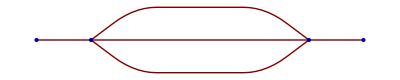

Using (14.3), the free particle propagator,

e143: Δ[k_]→1/(k^2+m^2-ⅈ ϵ)

⇒ ⅈ Π[k_]→-ⅈ (A k^2+B m^2)-1/2 ⅈ λ^2 IntegralOp[{{h1},{h2}},1/((h1^2+m^2-ⅈ ϵ) (h2^2+m^2-ⅈ ϵ) ((h1+h2+k)^2+m^2-ⅈ ϵ))]
⇒ ⅈ Π[k_]→-ⅈ (A k^2+B m^2)-1/2 ⅈ λ^2 xIntegrate[1/((h1^2+m^2-ⅈ ϵ) (h2^2+m^2-ⅈ ϵ) ((h1+h2+k)^2+m^2-ⅈ ϵ)),h1,h2]
Or with Feymann's formula
→ ⅈ Π[k_]→-ⅈ (A k^2+B m^2)-1/2 ⅈ λ^2 IntegralOp[{{h1},{h2},{x1},{x2},{x3}},(2 DiracDelta[-1+x1+x2+x3])/((x1 (h1^2+m^2-ⅈ ϵ)+x2 (h2^2+m^2-ⅈ ϵ)+x3 ((h1+h2+k)^2+m^2-ⅈ ϵ))^3)]

and the  conditions {Π[-m^2]→0,Π'[-m^2]→0} to set the values of A and B.

```mathematica
Print["Analogous with (14.4) where the perturbation term,Π, is derived from the 4 particle interaction term and where ",subAB={A->Z-1,B->Subscript[Z, m]-1}," and the coefficient is lumped ",Subscript[Z, λ] λ ω^3->λ];
DefPrint["a144",ⅈ Π[k_]->1/2(ⅈ λ)^2(-ⅈ)^3 IntegralOp[{{h1},{h2}},Δ[(h1)]Δ[(h1+h2+k)]Δ[h2]]
-ⅈ(A k^2+B m^2)];
Print["The diagram of this interaction looks like:"
];
GraphPlot[{1->2,2->3,2->3,2->3,3->4},VertexCoordinateRules->{1->{.08,0},2->{.1,0},3->{.18,0},4->{.2,0}}]

Print["Using (14.3), the free particle propagator,"];
DefPrint["e143",Δ[k_]->1/(k^2+m^2-ⅈ ϵ)];
Print[Imply,
tmp1=tmp=a144/.e143,Imply,
tmp1=tmp1/.IntegralOp[a_List,b_]:>xIntegrate[b,Flatten[a][[1]],Flatten[a][[2]]],
"\nOr with Feymann's formula",Yield,
tmp=tmp/.IntegralOp[a__List,1/(b_ c_ d_)]:>IntegralOp[Partition[Flatten[{a,{x1},{x2},{x3}}],1],2 DiracDelta[x1+x2+x3-1](x1 b+x2 c +x3 d)^-3]
];

Print["and the  conditions ",{Π[-m^2]->0,Π'[-m^2]->0}," to set the values of A and B."
];
```

```mathematica
Print["Use Cauchy Residue Theorem for integration:\n",
tmp1;Yield;
tmp=Extract[tmp1,Position[tmp1,xIntegrate[___]]][[1]],
"For the h1 integration there are 4 potential poles to be selected by the contours of {h1,h2} to be in part along the x-axis and the portion around the upper half-circle equal to 0.",Yield,
tmpn=tmp/.xIntegrate[a_,b_,c_]:>Denominator[a];Yield;
pole=Solve[tmpn==0,h1],
"\nOf these poles h1={2,4} are only in the upper-half plane since {k,h2}∈Reals."];
```

Use Cauchy Residue Theorem for integration:
xIntegrate[1/((h1^2+m^2-ⅈ ϵ) (h2^2+m^2-ⅈ ϵ) ((h1+h2+k)^2+m^2-ⅈ ϵ)),h1,h2]For the h1 integration there are 4 potential poles to be selected by the contours of {h1,h2} to be in part along the x-axis and the portion around the upper half-circle equal to 0.
→ {{h1→-h2-k-√(-m^2+ⅈ ϵ)},{h1→-h2-k+√(-m^2+ⅈ ϵ)},{h1→-√(-m^2+ⅈ ϵ)},{h1→√(-m^2+ⅈ ϵ)}}
Of these poles h1={2,4} are only in the upper-half plane since {k,h2}∈Reals.

```mathematica
ip=4;
Print["Investigate the h1 Residue at pole[",ip,"],
in the upper half plane: ",pole[[ip,1]],Yield,
res[ip]=tmp/.xIntegrate[a_,b_,c_]:>Residue[a,{pole[[ip,1,1]],pole[[ip,1,2]]}],Yield,
"The pole structure of h2 at h1 pole[",ip,"]:",
pole2=Solve[Denominator[res[ip]]==0,h2],
"\nOf these h2 poles {4} is the only one in the upper-half plane (assuming {k}∈Reals)",
ip2=4;
"\nSo the residue at ",pole2[[ip2,1]],Yield,
res2[ip,ip2]=Residue[res[ip],{pole2[[ip2,1,1]],pole2[[ip2,1,2]]}],Yield,
"So the {h1,h2}->{4,4} residue ",Yield,
res2[ip,ip2] /.ϵ->0//Simplify];
```

Investigate the h1 Residue at pole[4],
in the upper half plane: h1→√(-m^2+ⅈ ϵ)
→ 1/(2 (h2+k) (h2+k+2 √(-m^2+ⅈ ϵ)) (h2^2+m^2-ⅈ ϵ) √(-m^2+ⅈ ϵ))
→ The pole structure of h2 at h1 pole[4]:{{h2→-k},{h2→-k-2 √(-m^2+ⅈ ϵ)},{h2→-√(-m^2+ⅈ ϵ)},{h2→√(-m^2+ⅈ ϵ)}}
Of these h2 poles {4} is the only one in the upper-half plane (assuming {k}∈Reals)
So the residue at h2→√(-m^2+ⅈ ϵ)
→ -1/(4 (k+√(-m^2+ⅈ ϵ)) (k+3 √(-m^2+ⅈ ϵ)) (m^2-ⅈ ϵ))
→ So the {h1,h2}->{4,4} residue 
→ -1/(4 m^2 (k^2-3 m^2+4 k √(-m^2)))

```mathematica
ip=2;
Print["Investigate the h1 Residue at pole[",ip,"], 
in the upper half plane: ",pole[[ip,1]],Yield,
res[ip]=tmp/.xIntegrate[a_,b_,c_]:>Residue[a,{pole[[ip,1,1]],pole[[ip,1,2]]}],Yield,
"The pole structure of h2 at h1 pole[",ip,"]:",
pole2=Solve[Denominator[res[ip]]==0,h2],

"\nOf these h2 poles {2,4} are in the upper-half plane (assuming {k}∈Reals)",
ip2=2;
"\nSo the residue at ";pole2[[ip2,1]];Yield;
res2[ip,ip2]=Residue[res[ip],{pole2[[ip2,1,1]],pole2[[ip2,1,2]]}];
"\nThe {h1,h2}->{",ip,",",ip2,"} residue ",Yield,
res2[ip,ip2] /.ϵ->0//Simplify,
ip2=4;
"\nThe residue at ";pole2[[ip2,1]];Yield;
res2[ip,ip2]=Residue[res[ip],{pole2[[ip2,1,1]],pole2[[ip2,1,2]]}];
"\nThe {h1,h2}->{",ip,",",ip2,"} residue ",Yield,
res2[ip,ip2] /.ϵ->0//Simplify
];
```

Investigate the h1 Residue at pole[2], 
in the upper half plane: h1→-h2-k+√(-m^2+ⅈ ϵ)
→ -1/(2 (h2+k) (-h2-k+2 √(-m^2+ⅈ ϵ)) (h2^2+m^2-ⅈ ϵ) √(-m^2+ⅈ ϵ))
→ The pole structure of h2 at h1 pole[2]:{{h2→-k},{h2→-k+2 √(-m^2+ⅈ ϵ)},{h2→-√(-m^2+ⅈ ϵ)},{h2→√(-m^2+ⅈ ϵ)}}
Of these h2 poles {2,4} are in the upper-half plane (assuming {k}∈Reals)
The {h1,h2}->{2,2} residue 
→ 1/(4 m^2 (-k^2+3 m^2+4 k √(-m^2)))
The {h1,h2}->{2,4} residue 
→ -1/(4 m^2 (k^2+m^2))

```mathematica
Print["The sum of the residues, res2[4,4]+res2[2,2]+res2[2,4]",Yield,
resSum=res2[4,4]+res2[2,2]+res2[2,4]/.ϵ->0//FullSimplify
];
```

The sum of the residues, res2[4,4]+res2[2,2]+res2[2,4]
→ -3/(4 k^2 m^2+36 m^4)

```mathematica
ip2=1;ip=2;
Print["Does the pole at ",pole2[[ip2,1]]," contribute?"]
Print["The residue at {h1,h2}->{",ip,",",ip2,"} = ",
res2[ip,ip2]=Residue[res[ip],{pole2[[ip2,1,1]],pole2[[ip2,1,2]]}]
];
ip=4;
Print["The residue at {h1,h2}->{",ip,",",ip2,"} = ",
res2[ip,ip2]=Residue[res[ip],{pole2[[ip2,1,1]],pole2[[ip2,1,2]]}]
];
Print["These 2 terms cancel."];
```

Does the pole at h2→-k contribute?

The residue at {h1,h2}->{2,1} = 1/(4 (m^2-ⅈ ϵ) (k^2+m^2-ⅈ ϵ))

The residue at {h1,h2}->{4,1} = -1/(4 (m^2-ⅈ ϵ) (k^2+m^2-ⅈ ϵ))

These 2 terms cancel.

The correction to the propagator, Π

```mathematica
Print["Substituting back into a144 using the conditions (14.7) and (14.8) we can find relationships for {A,B}:",Yield,
subΠ=Map[#/ⅈ&,(a144/.IntegralOp[__]->(2 π ⅈ)^2 resSum)]//Simplify,
"\nThe consistency conditions",Imply,
conditions={0==D[(subΠ[[2]]/.k^2->kk),kk]/.kk->-m^2,
0==Π[ⅈ m]/.subΠ},Yield,
sub=Solve[conditions,{A,B}][[1]],"\n",
"The propagator correction is O(λ^2): \n",
subΠ/.sub//Simplify
];
```

Substituting back into a144 using the conditions (14.7) and (14.8) we can find relationships for {A,B}:
→ Π[k_]→-A k^2-B m^2-(3 π^2 λ^2)/(2 k^2 m^2+18 m^4)
The consistency conditions
⇒ {0==-A+(3 π^2 λ^2)/(128 m^6),0==A m^2-B m^2-(3 π^2 λ^2)/(16 m^4)}
→ {B→-(21 π^2 λ^2)/(128 m^6),A→(3 π^2 λ^2)/(128 m^6)}
The propagator correction is O(λ^2): 
Π[k_]→-(3 (k^2+m^2)^2 π^2 λ^2)/(128 m^6 (k^2+9 m^2))

Alternatively the propagator defined by (14.6)

```mathematica
DefPrint["e146",Δ[k_]->1/(k^2+m^2-ⅈ ϵ-Π[k])]
tmp=e146/.subΠ
tmp=tmp/.A->Subscript[κ, A] λ/.B->Subscript[κ, B] λ
tmp=Series[tmp[[2]],{λ,0,1}]//Normal
"Residue==1 condition at pole k^2==-m^2 on propagator "
tmp[[1]]==tmp;
Solve[%,Subscript[κ, A]][[1]]/.k->ⅈ m
"This is different from above two determinations of κ_A and κ_B.  This final determination is independent of λ so seems incorrect. "
```

e146: Δ[k_]→1/(k^2+m^2-ⅈ ϵ-Π[k])

Δ[k_]→1/(k^2+A k^2+m^2+B m^2-ⅈ ϵ+(3 π^2 λ^2)/(2 k^2 m^2+18 m^4))

Δ[k_]→1/(k^2+m^2-ⅈ ϵ+(3 π^2 λ^2)/(2 k^2 m^2+18 m^4)+k^2 λ κ_A+m^2 λ κ_B)

1/(k^2+m^2-ⅈ ϵ)+(λ (-k^2 κ_A-m^2 κ_B))/((k^2+m^2-ⅈ ϵ)^2)

Residue==1 condition at pole k^2==-m^2 on propagator

{κ_A→κ_B}

This is different from above two determinations of κ_A and κ_B.  This final determination is independent of λ so seems incorrect.